# Symbolic Regression of Pendulum Data

## Introduction

## Lagrangians

### Euler Lagrange Equations

### Converting Expression from Cloure.

## Single Pendulum

### Theoretical Lagrangian

Theoretical single pendulum Lagrangian is of the form:

(L=1/2 mr^2(dθ/dt))^2-mgr(1-cosθ)

```mathematica
mass=1
length=1
gravity=1

simplepenlag[theta_,thetaprime_]:=(1/2*mass*length^2*thetaprime^2)-mass*gravity*length*(1-Cos[theta])
```

1

1

1

```mathematica
singpendata = Import["/Users/joelrussell/Documents/Imperial/Year_4/Masters_Project/Code/joel_flow/flow/data/mma_pendulum_large.csv"] //Short

theta={#⟦1⟧&/@singpendata} 
thetaprime={#⟦2⟧&/@singpendata}
```

(«1»)

{{2.98451,-2.71051×10^-20}}

{{2.98137,-0.0629866}}

```mathematica
ListPlot[theta,AxesLabel->θ]
ListPlot[thetaprime,AxesLabel->θ']
```

-Graphics-

-Graphics-

```mathematica
ListPlot[simplepenlag[theta,thetaprime],AxesLabel->lagrangian]
```

-Graphics-

### Numerical Lagrangian Expressions

```mathematica
triallag1[theta_,omega_]:=Times[Times[0.022210588271571317, Plus[Plus[Plus[Plus[Plus[Plus[Plus[Cos[omega], Cos[theta]], Times[Cos[theta], 0.6247552574671112]], Cos[theta]], Times[Plus[Plus[Plus[Plus[Cos[omega], Cos[theta]], Cos[theta]], Cos[theta]], Cos[theta]], Cos[theta]]], omega], omega], Cos[theta]]], Sin[theta]]
```

```mathematica
run1[theta_,omega_]:=Plus[Sin[theta], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.12642579887098596], Times[omega, omega]]]]
run2[theta_,omega_]:=Times[Plus[Plus[Sin[theta], Subtract[Plus[Sin[theta], 1.9273329585287498], Sin[theta]]], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.12641372676463694], Times[omega, omega]]]], 0.06703977631709543]

ListPlot[run1[theta,thetaprime]]
ListPlot[run2[theta,thetaprime]]
```

-Graphics-

-Graphics-

### Euler Lagrange Equations

```mathematica
Needs["VariationalMethods`"]
```

#### THEORETICAL

1

1

9.8

Theoretical Values with Algebraic Representations of m g and l

mgr (1-cos(θ(t)))+1/2 mr^2 (θ'(t))^2

mgr sin(θ(t))-mr^2 θ''(t)==0

{{θ''(t)→(mgr sin(θ(t)))/mr^2}}

1/2 (θ'(t))^2+9.8 (1-cos(θ(t)))

9.8 sin(θ(t))-θ''(t)==0

{9.8 sin(θ(t))-θ''(t)==0,θ(0)==2.98451,θ'(0)==-2.71051×10^-20}

{{θ(t)→InterpolatingFunction[{{0., 30.}}, <>](t)}}

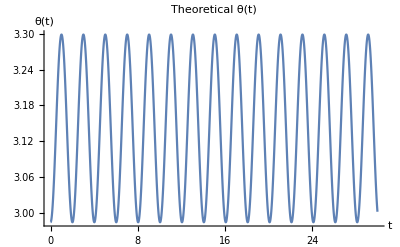

```mathematica
Clear[m,l,g]

m = 1
l = 1
g = 9.8

"Theoretical Values with Algebraic Representations of m g and l"

theorylag = 1/2 mr^2 θ'[t]^2+mgr(1-Cos[θ[t]])
theoryEL = EulerEquations[theorylag,θ[t],t]
theorysol = Solve[theoryEL,θ''[t]]

theorylagn = 1/2 m*l^2*θ'[t]^2+m*g*l*(1-Cos[θ[t]])
ELth = EulerEquations[theorylagn,θ[t],t]

s =Join[List[ELth],{θ[0] == 2.9845130209103,θ'[0] == -2.71050543121376*10^-20}]

theorysoln = NDSolve[s,θ[t],{t,0,30}]

Plot[Evaluate[θ[t]/.theorysoln],{t,0,30},PlotRange->All,PlotLabel->Theoretical θ[t],AxesLabel->{t,θ[t]}]
```

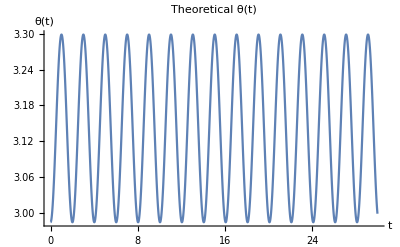

```mathematica
"theorylag[mass_,length_,gravity_] := 1/2mass*length^2*"
```

theorylag[mass_,length_,gravity_] := 1/2mass*length^2*

#### EXPERIMENTAL

0.0670398 (0.126401 omega^2 sin(theta)+sin(theta)+sin(theta) cos(theta))

0.0670398 (0.126401 sin(theta) (θ'(t))^2+sin(theta)+sin(theta) cos(theta))

0.0670398 (0.126401 (θ'(t))^2 sin(θ(t))+sin(θ(t))+sin(θ(t)) cos(θ(t)))

-0.0169478 θ''(t) sin(θ(t))-0.00847391 (θ'(t))^2 cos(θ(t))-0.0670398 sin^2(θ(t))+0.0670398 cos^2(θ(t))+0.0670398 cos(θ(t))==0

{-0.0169478 θ''(t) sin(θ(t))-0.00847391 (θ'(t))^2 cos(θ(t))-0.0670398 sin^2(θ(t))+0.0670398 cos^2(θ(t))+0.0670398 cos(θ(t))==0,θ(0)==2.98451,θ'(0)==-2.71051×10^-20}

{{θ(t)→InterpolatingFunction[{{0., 30.}}, <>](t)}}

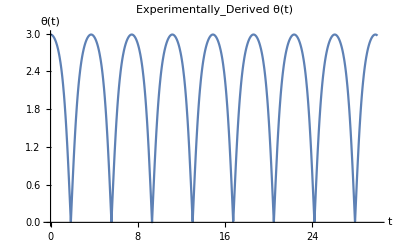

```mathematica
Clear[theta]

L= Times[Plus[Sin[theta], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.1264012221818857], Times[omega, omega]]]], 0.06703977631709543]

L = L/.omega->θ'[t]
L = L/.theta->θ[t]

ELexp = EulerEquations[L,θ[t],t]

Clear[s]

s =Join[List[ELexp],{θ[0] == 2.9845130209103,θ'[0] == -2.71050543121376*10^-20}]

expsoln = NDSolve[s,θ[t],{t,0,30}]

Plot[Evaluate[θ[t]/.expsoln],{t,0,30},PlotRange->All,PlotLabel->Experimentally_Derived θ[t],AxesLabel->{t,θ[t]}]
```

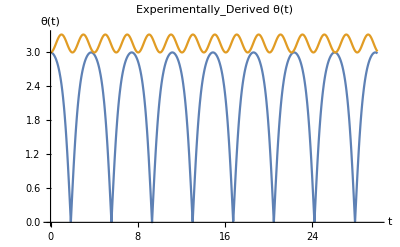

```mathematica
Plot[{Evaluate[θ[t]/.expsoln], Evaluate[θ[t]/.theorysoln]},{t,0,30},PlotRange->All,PlotLabel->Experimentally_Derived θ[t],AxesLabel->{t,θ[t]}]
```

## Double Pendulum

### Theoretical Lagrangian

Theoretical analytical double pendulum lagrangian is of the form:

L = 1/2 (m_1+m_2)(l_1^2(dθ_1/dt))^2+1/2 m_2(l_2^2(dθ_2/dt))^2+m_2 l_1 l_2(dθ_1/dt)(dθ_2/dt)cos(θ_1-θ_2)+(m_1+m_2)gl_1 cos(θ_1)+m_2 gl_2 cos(θ_2)

```mathematica
"Parameters:"
Subscript[m, 1] = 1 
Subscript[l, 1] = 1
Subscript[m, 2] = 1
Subscript[l, 2] = 1
g = 9.8

Clear[theorylag]
Clear[theoryEL]
Clear[theorysol]

theorylag = 1/2(m1+m2)l1^2*(Subscript[θ, 1]'[t])^2+1/2 m1*l2^2*(Subscript[θ, 2]'[t])^2+m2*l1*l2*(Subscript[θ, 1]'[t])*(Subscript[θ, 2]'[t])cos(Subscript[θ, 1][t]-Subscript[θ, 2][t])+(m1+m2)gr*Subscript[l, 1]*cos(Subscript[θ, 1][t])+m2*gr*l2*cos(Subscript[θ, 2][t])

theoryEL = EulerEquations[theorylag,{Subscript[θ, 1][t],Subscript[θ, 2][t]},t]

theorysol = Solve[theoryEL,{Subscript[θ, 1]''[t],Subscript[θ, 2]''[t]}]



Clear[theorylagn]
Clear[ELth]
Clear[s]
Clear[theorysoln]

theorylagn = 1/2(Subscript[m, 1]+Subscript[m, 2])l1^2*(Subscript[θ, 1]'[t])^2+1/2 Subscript[m, 2]*Subscript[l, 2]^2*(Subscript[θ, 2]'[t])^2+Subscript[m, 2]*Subscript[l, 1]*Subscript[l, 2]*(Subscript[θ, 1]'[t])*(Subscript[θ, 2]'[t])cos(Subscript[θ, 1][t]-Subscript[θ, 2][t])+(Subscript[m, 1]+Subscript[m, 2])g*Subscript[l, 1]*cos(Subscript[θ, 1][t])+Subscript[m, 2]*g*Subscript[l, 2]*cos(Subscript[θ, 2][t])
ELth = EulerEquations[theorylagn,θ[t],t]

s =Join[List[ELth],{θ[0] == 2.9845130209103,θ'[0] == -2.71050543121376*10^-20}]

theorysoln = NDSolve[s,{Subscript[θ, 1][t],Subscript[θ, 2][t]},{t,0,30}]

Plot[Evaluate[θ[t]/.theorysoln],{t,0,30},PlotRange->All,PlotLabel->Theoretical θ[t],AxesLabel->{t,θ[t]}]
```

Parameters:

1

1

1

«1 more identical outputs»

9.8

2 gr cos θ_1(t)+gr cos θ_2(t)+(θ_1'(t))^2+1/2 (θ_2'(t))^2+cos (θ_1(t)-θ_2(t)) θ_2'(t) θ_1'(t)

{cos (2 gr-θ_1(t) θ_2''(t)+θ_2(t) θ_2''(t))+cos (θ_2'(t))^2-2 θ_1''(t)==0,gr cos-cos (θ_1'(t))^2-θ_2''(t)-cos θ_1(t) θ_1''(t)+cos θ_2(t) θ_1''(t)==0}

{{θ_1''(t)→-(-(cos θ_2(t)-cos θ_1(t)) (gr cos-cos (θ_1'(t))^2)-2 gr cos-cos (θ_2'(t))^2)/(2-(cos θ_2(t)-cos θ_1(t))^2),θ_2''(t)→-((-2 gr cos^2 θ_1(t)+2 gr cos^2 θ_2(t)+2 gr cos+cos^2 (-θ_1(t)) (θ_2'(t))^2+cos^2 θ_2(t) (θ_2'(t))^2-2 cos (θ_1'(t))^2)/(cos^2 (θ_1(t))^2+cos^2 (θ_2(t))^2-2 cos^2 θ_1(t) θ_2(t)-2))}}

(θ_1'(t))^2+1/2 (θ_2'(t))^2+cos (θ_1(t)-θ_2(t)) θ_2'(t) θ_1'(t)+19.6 cos θ_1(t)+9.8 cos θ_2(t)

EulerEquations::args: EulerEquations takes a single integrand, a function or list of functions, and a list of variables as input.

EulerEquations((θ_1'(t))^2+1/2 (θ_2'(t))^2+cos (θ_1(t)-θ_2(t)) θ_2'(t) θ_1'(t)+19.6 cos θ_1(t)+9.8 cos θ_2(t),θ(t),t)

{EulerEquations((θ_1'(t))^2+1/2 (θ_2'(t))^2+cos (θ_1(t)-θ_2(t)) θ_2'(t) θ_1'(t)+19.6 cos θ_1(t)+9.8 cos θ_2(t),θ(t),t),θ(0)==2.98451,θ'(0)==-2.71051×10^-20}

NDSolve::deqn: Equation or list of equations expected instead of EulerEquations(19.6 cos θ_1(t)+9.8 cos θ_2(t)+(θ_1'(t))^2+cos (θ_1(t)-θ_2(t)) θ_1'(t) θ_2'(t)+1/2 (θ_2'(t))^2,θ(t),t) in the first argument {EulerEquations(19.6 cos θ_1(t)+9.8 cos θ_2(t)+(θ_1'(t))^2+cos (θ_1(t)-θ_2(t)) θ_1'(t) θ_2'(t)+1/2 (θ_2'(t))^2,θ(t),t),θ(0)==2.98451,θ'(0)==-2.71051×10^-20}.

NDSolve[{EulerEquations((θ_1'(t))^2+1/2 (θ_2'(t))^2+cos (θ_1(t)-θ_2(t)) θ_2'(t) θ_1'(t)+19.6 cos θ_1(t)+9.8 cos θ_2(t),θ(t),t),θ(0)==2.98451,θ'(0)==-2.71051×10^-20},{θ_1(t),θ_2(t)},{t,0,30}]

ReplaceAll::reps: {NDSolve[{EulerEquations(19.6 cos θ_1(t)+9.8 cos θ_2(t)+(Subscript[«2»]'(t))^2+cos (Subscript[«2»][«1»]+Times[«2»]) Subscript[«2»]'(t) Subscript[«2»]'(t)+1/2 ((«1»)^(«1»)(«1»))^2,θ(t),t),θ(0)==2.98451,θ'(0)==-2.71051×10^-20},{θ_1(t),θ_2(t)},{t,0,30}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

EulerEquations::args: EulerEquations takes a single integrand, a function or list of functions, and a list of variables as input.

NDSolve::dsvar: 0.000612857 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{θ_1(0.000612857),θ_2(0.000612857)},{0.000612857,0,30}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

EulerEquations::args: EulerEquations takes a single integrand, a function or list of functions, and a list of variables as input.

NDSolve::dsvar: 0.000612857 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{θ_1(0.000612857),θ_2(0.000612857)},{0.000612857,0.,30.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

EulerEquations::args: EulerEquations takes a single integrand, a function or list of functions, and a list of variables as input.

General::stop: Further output of EulerEquations::args will be suppressed during this calculation.

NDSolve::dsvar: 0.612858 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

Parameters:

1

1

1

«1 more identical outputs»

9.8

(θ_1'(t))^2

### Euler-Lagrange Equations

#### Theoretical

```mathematica
Simplify[Times[Times[Times[Times[Times[theta2, theta2], Times[Times[theta2, theta2], Times[Times[Times[theta2, theta2], Times[theta1, theta1]], Times[Times[Cos[omega1], Times[theta1, theta1]], Times[theta1, theta1]]]]], Times[theta1, theta1]], Times[Times[Times[theta2, theta2], Subtract[Sin[theta1], theta1]], Cos[omega2]]], Times[Times[theta2, theta2], Times[Times[theta2, theta2], Times[theta1, theta1]]]]]
```

theta1^10 theta2^12 cos(omega1) cos(omega2) (sin(theta1)-theta1)